## Oron’s 3D Case Fig 2 solved with BDF1 method. Mass conservation is checked as well.

```mathematica
$HistoryLength=0;
Needs["VectorAnalysis`"]
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Clear[Eq0,EvapThickFilm,h,Bo,ϵ,K1,δ,Bi,m,r]
Eq0[h_,{Bo_,ϵ_,K1_,δ_,Bi_,m_,r_}]:=D[h, t]+Div[-h^3 Bo Grad[h]+h^3 Grad[Laplacian[h]]+(δ h^3)/(Bi h+K1)^3 Grad[h]+m(h/(K1+Bi h))^2 Grad[h]]+ϵ/(Bi h+K1) + (r)D[D[(h^2/(K1+Bi h)),x] h^3,x] ==0;
SetCoordinates[Cartesian[x,y,z]];
EvapThickFilm[Bo_,ϵ_,K1_,δ_,Bi_,m_,r_]:=Eq0[h[x,y,t],{Bo,ϵ,K1,δ,Bi,m,r}];
TraditionalForm[EvapThickFilm[Bo,ϵ,K1,δ,Bi,m,r]];
```

```mathematica
L=2*92.389; TMax=3100*100;
Off[NDSolve::mxsst];
Clear[Kvar];
Kvar[t_]:=  Piecewise[{{1,t≤1},{2,t>1}}]
g[x_,y_]:=g[x,y]=1 -0.05RandomReal[1,{30,30}];
(*Ktemp = Array[0.001+0.001#^2&,13]*)
hSol=h/.NDSolve[{
(*Bo,ϵ,K1,δ,Bi,m,r*)

EvapThickFilm[0.003,0,1,0,1,0.025,0],
h[0,y,t]==h[L,y,t],
h[x,0,t]==h[x,L,t],
(*h[x,y,0] == 1.1+Cos[x] Sin[2y] *)
h[x,y,0]==g[x,y]
},
h,
{x, 0, L},
{y,0, L},
{t, 0, TMax},
Method->{"BDF","MaxDifferenceOrder"->1},
MaxStepFraction->1/50
]⟦1⟧
```

InterpolatingFunction[{{0.,184.778},{0.,184.778},{0.,310000.}},<>]

```mathematica
hGrid = InterpolatingFunctionGrid[hSol];
{TMin,TRup}=InterpolatingFunctionDomain[hSol]⟦3⟧
Length[hGrid]
{nX,nY,nT}=Drop[Dimensions[hGrid],-1]
```

{0.,310000.}

51

{51,51,52}

0.

-Graphics3D-

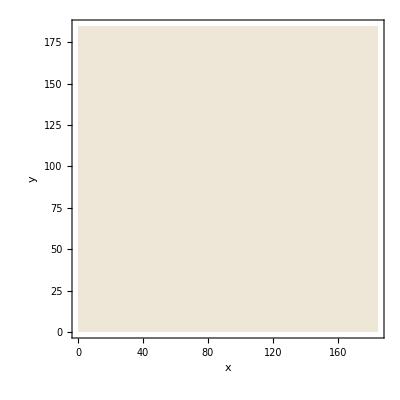

```mathematica
fac=0.0

Plot3D[hSol[x,y,fac*TRup],{x,0,L},{y, 0, L},

PlotRange->{{0,L},{0,L},{0,2}},
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
ContourPlot[
hSol[x,y,fac*TRup],{x,0,L},{y,0,L},
PlotRange->{{0,L},{0,L},{0,2}},
AxesLabel->{"x","y","h"},
BaseStyle->{FontWeight->"Bold",FontSize->18},
Contours->50
]
```

```mathematica
Manipulate[
{
Plot3D[hSol[x,y,fac*TMax],{x,0,L},{y, 0, L},
PlotRange->{{0,L},{0,L},{0,4}},
AxesLabel->{"x","y","h"},
PlotLabel->"t=TRup"]
},
{fac,0,1}
]
```

Mass conservation check :

```mathematica
L=2*92.389;
TMax=2491.29*100;
Off[NDSolve::mxsst];
hSol[x_?NumericQ,y_?NumericQ,t_?NumericQ]=h[x,y,t]/.NDSolve[{
(*Bo,ϵ,K1,δ,Bi,m,r*)

EvapThickFilm[0.003,0,1,0,1,0.025,0],
h[0,y,t]==h[L,y,t],
h[x,0,t]==h[x,L,t],
(*h[x,y,0] == 1.1+Cos[x] Sin[2y] *)
h[x,y,0]==1+(-0.25 Cos[2π x/L] -0.25 Sin[2 π x/L])Cos[2 π y/L]
},
h,
{x, 0, L},
{y,0, L},
{t, 0, TMax},
Method->{"BDF","MaxDifferenceOrder"->1},
MaxStepFraction->1/50
]⟦1⟧
```

Set::write: Tag InterpolatingFunction in TagBox[InterpolatingFunction[{{0.`, 184.778`}, {0.`, 184.778`}, {0.`, 249129.`}}, {4, 21, 1, {50, 50, 150}, {8, 8, 4}, 0, {1, 1, 0}, 0, 0, Automatic}, {« 1 »}, {Developer`PackedArrayForm, {« 1 »}, {0.75`, 2.147483584`*^9, 2.147483584`*^9, -1.2167624812232689`*^-6, 0.7499808435352201`, « 42 », -1.1734077359615068`*^-6, 0.7464811238996648`, 2.147483584`*^9, « 1499950 »}}, {Automatic, Automatic, Automatic}], False, Rule[Editable, False]] is Protected.

InterpolatingFunction[{{0.,184.778},{0.,184.778},{0.,249129.}},<>][x,y,t]

```mathematica
NIntegrate[hSol[x,y,0.1*TMax],{x,0,L},{y,0,L}]
```